#### This program is based on the paper titled ‘Solving Multi-dimensional European Option Pricing Problems by Integrals of the Inverse Quadratic Radial Basis Function on Non-uniform Meshes’ for the 4D European option pricing problem. It is intended to help readers achieve better reliability and obtain similar simulations and results. Further inquiries can be directed to Fazlollah Soleymani, the corresponding author of this paper.

The whole computational time is = 0.7648223

The final sought-after solution = 13.631652567

The absolute error is = 2.73474×10^-2

The relative error is = 2.00215×10^-3

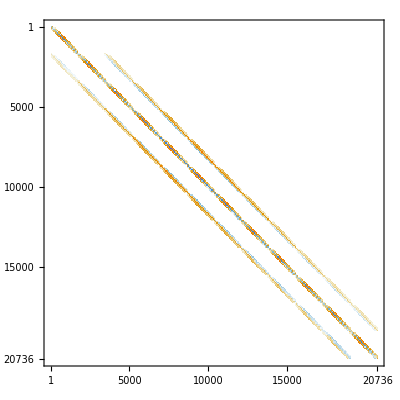

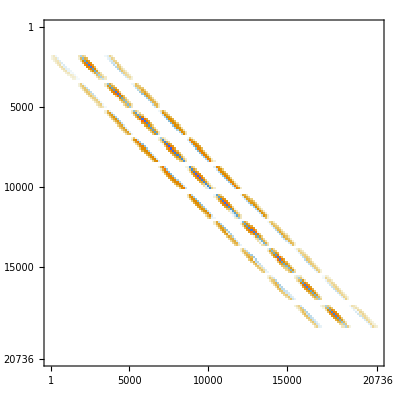

```mathematica
ClearAll["Global`*"];
t1=AbsoluteTime[];

TT=1.;n1=n2=n3=n4=12;NN=n1*n2*n3*n4;Q=100.;
ksi1=1/4;ksi2=1/4;ksi3=1/4;ksi4=1/4;ro1=0.5;ro2=0.5;ro3=0.5;ro4=0.5;
sig1=0.3;sig2=0.35;sig3=0.4;sig4=0.45;r=0.04;r1=0.01;ga1=0;ga2=0;ga3=0;ga4=0;

ymin=0; ymax=6Q;d1=Q/10;yleft=Max[0.5,Exp[-r1*TT]]*Q;yright=Q;
ksiMin=ArcSinh[(ymin-yleft)/d1];kint=(yright-yleft)/d1;ksiMax=kint+ArcSinh[(ymax-yright)/d1];
zeta=Range[ksiMin,ksiMax,(ksiMax-ksiMin)/(n1-1)];
fun[ks_]:=Which[ksiMin≤ ks<0,yleft+d1*Sinh[ks],0≤ ks≤ kint,
yleft+d1*ks,kint<ks≤ksiMax,yright+d1*Sinh[ks-kint]];
pgrid1=zgrid1=ygrid1=xgrid1=Chop@Table[fun[zeta[[i]]],{i,n1}];
origrid= Flatten[Outer[List,xgrid1,ygrid1,zgrid1,pgrid1],3];

(***********************************)
hh=Differences[xgrid1];ww=Table[hh[[i+1]]/hh[[i]],{i,1,Length[hh]-1}];
{Max[hh],c=3Max[hh]};
A1d1=Join[Table[(ww [[i-1]] (-18+(hh[[i-1]]^2 (3 (1+ww [[i-1]] )+(4-16 ww [[i-1]] ) Log[c]))/(c^2 (-1+2 Log[c]))))/(18 hh[[i-1]] (1+ww [[i-1]] )),{i,2,n1-1}],{ -1/hh[[Length[hh]]]+hh[[Length[hh]]]/c^2}];
A1d2=Join[{-1/hh[[1]]+hh[[1]]/c^2},Table[(-1+ww[[i-1]])/(hh[[i-1]] ww[[i-1]])+(hh[[i-1]] (-1+ww[[i-1]]) (-3+16 Log[c]))/(18 c^2 (-1+2 Log[c])),{i,2,n1-1}],{1/hh[[Length[hh]]]}];
A1d3=Join[{1/hh[[1]]},Table[(18/ww[[i-1]]-(hh[[i-1]]^2 (3 (1+ww[[i-1]])+4 (-4+ww[[i-1]]) Log[c]))/(c^2 (-1+2 Log[c])))/(18 hh[[i-1]] (1+ww[[i-1]])),{i,2,n1-1}]];
(*{Max[hh],c=3Max[hh]}*)
A2d1=Join[Table[(18/hh[[i-1]]^2+(-3+3 (-1+ww[[i-1]]) ww[[i-1]]-4 (1+2 ww[[i-1]](-7+2 ww[[i-1]])) Log[c])/(c^2 (-1+2 Log[c])))/(9 (1+ww[[i-1]])),{i,2,n1-1}],{-4/c^2}];
A2d2=Join[{-4/c^2},Table[(-18/hh[[i-1]]^2+(-3-3 (-3+ww[[i-1]]) ww[[i-1]]+4 (-4+ww[[i-1]]) (-1+4 ww[[i-1]]) Log[c])/(c^2 (-1+2 Log[c])))/(9 ww[[i-1]]),{i,2,n1-1}],{2/c^2}];
A2d3=Join[{2/c^2},Table[(18/hh[[i-1]]^2+(-3 (-1+ww[[i-1]]+ww[[i-1]]^2)-4 (4+(-14+ww[[i-1]]) ww[[i-1]]) Log[c])/(c^2 (-1+2 Log[c])))/(9 ww[[i-1]](1+ww[[i-1]])),{i,2,n1-1}]];

DM1=Chop@SparseArray[{Band[{1,1}]->A1d2,Band[{2,1}]->A1d1,Band[{1,2}]->A1d3},{n1,n1}];
DM2=Chop@SparseArray[{Band[{1,1}]->A2d2,Band[{2,1}]->A2d1,Band[{1,2}]->A2d3},{n1,n1}];
(***********************************)
Idx=SparseArray[{{i_,i_}->1.},{n1,n1},0]; Idy=SparseArray[{{i_,i_}->1.},{n2,n2},0]; 
Idz=SparseArray[{{i_,i_}->1.},{n3,n3},0];Idp=SparseArray[{{i_,i_}->1.},{n4,n4},0];
XX=KroneckerProduct[(SparseArray@DiagonalMatrix@xgrid1),Idy,Idz,Idp]; 
YY=KroneckerProduct[Idx,(SparseArray@DiagonalMatrix@ygrid1),Idz,Idp]; 
ZZ=KroneckerProduct[Idx,Idy,(SparseArray@DiagonalMatrix@zgrid1),Idp];
PP=KroneckerProduct[Idx,Idy,Idz,(SparseArray@DiagonalMatrix@pgrid1)];
Id=KroneckerProduct[Idx,Idy,Idz,Idp];
dudx=DM1;dudy=DM1;dudz=DM1;dudp=DM1;d2udx2=DM2;d2udy2=DM2;d2udz2=DM2;d2udp2=DM2;
(***********************************)
A=Chop@SparseArray@(
(1/2 sig1^2XX^2).KroneckerProduct[d2udx2,Idy,Idz,Idp]
+(1/2 sig2^2 YY^2).KroneckerProduct[Idx,d2udy2,Idz,Idp]
+(1/2 sig3^2 ZZ^2).KroneckerProduct[Idx,Idy,d2udz2,Idp]
+(1/2 sig4^2 PP^2).KroneckerProduct[Idx,Idy,Idz,d2udp2]
+(ro1*(sig1*sig2))*(XX.YY).KroneckerProduct[dudx,dudy,Idz,Idp]
+(ro2*(sig2*sig3))*(YY.ZZ).KroneckerProduct[Idx,dudy,dudz,Idp]
+(ro3*(sig1*sig3))*(XX.ZZ).KroneckerProduct[dudx,Idy,dudz,Idp]
+(ro4*(sig1*sig4))*(XX.PP).KroneckerProduct[dudx,Idy,Idz,dudp]
+(ro4*(sig2*sig4))*(YY.PP).KroneckerProduct[Idx,dudy,Idz,dudp]
+(ro4*(sig3*sig4))*(ZZ.PP).KroneckerProduct[Idx,Idy,dudz,dudp]
+((r-ga1)*XX).KroneckerProduct[dudx,Idy,Idz,Idp]
+((r-ga2)*YY).KroneckerProduct[Idx,dudy,Idz,Idp]
+((r-ga3)*ZZ).KroneckerProduct[Idx,Idy,dudz,Idp]
+((r-ga4)*PP).KroneckerProduct[Idx,Idy,Idz,dudp]
-r Id
);
(***********************************)
U[t_]=Flatten@Table[Subscript[u, i,j,k,l][t],{i,n1},{j,n2},{k,n3},{l,n4}];
payoff=Flatten@Table[Max[(ksi1*xgrid1[[i]]+ksi2*ygrid1[[j]]+ksi3*zgrid1[[k]]+ksi4*pgrid1[[l]])-Q,0],{i,n1},{j,n2},{k,n3},{l,n4}];
initc=Thread[v[0]==payoff];
A0=A;
(***********************************)
index1=Flatten[Table[{i,j,k,l},{i,n1},{j,n2},{k,n3},{l,n4}],3];
Table[ind=index1[[l]];
If[(ind[[1]]==1||ind[[1]]==n1)||
(ind[[2]]==1||ind[[2]]==n2)||
(ind[[3]]==1||ind[[3]]==n3)||
(ind[[4]]==1||ind[[4]]==n4),var[l]=0,var[l]=l
],{l,Length@index1}];

bounindex=Table[var[l],{l,Length@index1}];
delete=Pick[Range[NN],bounindex,0];
len=Length[delete];
A[[delete]]=SparseArray[{},{len,NN}];
(***********************************)
sol2=MatrixExp[A,payoff,Method->"Krylov"];
ClearAll[hh,dudx,  dudy,dudz,dudp,DM1,DM2,d2udx2, d2udy2, d2udz2,d2udp2];
set1=Flatten[Table[{Flatten@{origrid[[i]],sol2[[i]]}},{i,Length[payoff]}],1];
t2=AbsoluteTime[]-t1;
Print["The whole computational time is = ",t2];
(***********************************)
gg=Interpolation@set1;
Print["The final sought-after solution = ",SetAccuracy[gg[Q,Q,Q,Q],10]];
Print["The absolute error is = ",ScientificForm@Abs[13.659-gg[Q,Q,Q,Q]]];
Print["The relative error is = ",ScientificForm@Abs[(13.659-gg[Q,Q,Q,Q])/13.659]];
MatrixPlot[A0] 
MatrixPlot[A]
```